# Cálculo de pârametros unitários de uma linha de transmissão em circuito duplo

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2021/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=80 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

## Circuito 230kV

Coordenadas dos condutores

```mathematica
yc={22.15185227641591,28.15185227641591,34.15185227641591,22.15185227641591,28.15185227641591,34.15185227641591,39.15185227641591,39.15185227641591};
xc={-4.3,-4.3,-4.3,4.3,4.3,4.3,-3.8,3.8};
```

Dados condutores de fase -- Grossbeak

```mathematica
r0=7.456 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 12.573 10^-3;
ρϕ=29.538 10^-9;  (* [Ω/m] *)
Rdc= 0.00009173953403774036;
```

Dados dos cabos pararraios

```mathematica
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},All},FrameTicks->{{-10,-5, 0,5, 10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-

## Função para cálculo das matrizes

faz parte do arquivo LineCableParam2020.wl

```mathematica
(* impedancia interna de condutores tubulares *)
ZintTubo[Omega_, Rhoc_, rf_, rint_, Mur_: 1, Mu_: (4.*Pi)/10^7] := 
 With[{Etac = N[Sqrt[(I*Omega*Mur*Mu)/Rhoc]], ri = rint + 10^-6}, 
  With[{Den = 
     BesselK[1, Etac*ri]*BesselI[1, Etac*rf] - 
      BesselK[1, Etac*rf]*BesselI[1, Etac*ri], 
    Num = BesselK[1, Etac*ri]*BesselI[0, Etac*rf] + 
      BesselK[0, Etac*rf]*BesselI[1, Etac*ri]}, ((Rhoc*Etac)*
      Num)/((2*Pi*rf)*Den)]]
      
(* impedancia interna de condutor sem alma de aco *)
(* impedancia interna de condutores cilindricos *) 
(*Mur=90 para cables de aco*)    
Zin[Omega_, Rhopr_, rpr_, Mur_:90, Mu_:(4*Pi)/10^7] := 
    With[{Etapr = Sqrt[(I*Omega*Mu*Mur)/Rhopr]}, 
         ((Etapr*Rhopr)*BesselI[0, Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]
```

```mathematica
(* internal impedance of cylindrical conductors *)
zintc= Compile[{{omega, _Complex}, {Rhoc, _Real}, {rf, _Real}, {ri,_Real}, {Mur, _Real}},
 ZintTubo[omega, Rhoc, rf, ri, Mur]];
 
zic= Compile[{{omega,_Complex},{rhoc, _Real},{rf, _Real}, {mur,_Real}},
	 Zin[omega, rhoc, rf, mur]];
```

```mathematica
(*  ground wires are not explicitly considered so we include their effects via Kron Reduction -- matrizes devem estar no formato de impedancia *)        
eliprc = Compile[{{m,_Complex,2},{nc,_Integer},{np,_Integer}},
	            Take[Inverse[m], nc - np, nc - np]
	            ];
```

```mathematica
(* case  2: ground wires and unbundled conductors *)
cZYlt[omega_,(x_)?VectorQ, (y_)?VectorQ, sigmas_, rdc_,rf_,rint_, npr_, rdcpr_, rpr_]:=
    Module[{mu=4*Pi*10^-7, eps=8.854*10^-12, nc=Length[x],  nf, rhoc, rhopr, mp, zin, ze, Z1, Y1},
    	
    nf= IntegerPart[(nc-npr)];
    rhoc= rdc*Pi*(rf^2-rint^2);
    rhopr= rdcpr*Pi*rpr^2;
   
   If[ rint != 0, 
   zin= DiagonalMatrix[
   	    Join[zintc[omega, rhoc, rf, rint, 1] Table[1, {i, nc - npr}], 
             zic[omega, rhopr, rpr, 90] Table[1, {i, npr}]]
             ],
   zin= DiagonalMatrix[
   	    Join[zic[omega, rhoc, rf, 1] Table[1, {i, nc - npr}], 
             zic[omega, rhopr, rpr,90] Table[1, {i, npr}]]
             ];
   ];
   
             
   ze= I omega mu/(2 Pi) With[{p = Sqrt[1/(I*omega*mu*sigmas)]}, 
         Table[If[i != j, 
         	  (Log[((x[[i]] - x[[j]])^2 + (2*p + y[[i]] + y[[j]])^2)/((x[[i]] - x[[j]])^2 +(y[[i]] - y[[j]])^2)])/(2), 
              If[i <= nc - npr, 
               (Log[(2*(y[[i]] + p))/rf]), 
               (Log[(2*(y[[i]] + p))/rpr])]],
         {i, 1, nc}, 
         {j, 1, nc}]];
         
    Z1 = Inverse[eliprc[zin+ze, nc, npr]];     
         
    mp= Table[If[i != j, 
   	    (1/2)*Log[((x[[i]] - x[[j]])^2 + (y[[i]] + y[[j]])^2)/((x[[i]] - x[[j]])^2 + (y[[i]] - y[[j]])^2)], 
        If[i <= nc - npr, Log[(2*y[[i]])/rf], 
        Log[(2*y[[i]])/rpr]]],{i, 1, nc}, {j, 1, nc}];
          
    Y1=3.0*10^-12 DiagonalMatrix[Table[1,{nf}]] + I omega*2*Pi*eps* eliprc[mp, nc, npr];
          
    {Z1, Y1}       
];
```

## Cálculo das matrizes

```mathematica
ω= 2. π 60;
ρs= 1000.;
npr = 2;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc,yc,1/ρs, Rdc,r1,r0, npr, Rdcpr, rpr];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.184661+0.898712 ⅈ | 0.0955069+0.421026 ⅈ | 0.0999152+0.36468 ⅈ | 0.0926263+0.39654 ⅈ | 0.0954839+0.378943 ⅈ | 0.0998478+0.349087 ⅈ
0.0955069+0.421026 ⅈ | 0.190654+0.893237 ⅈ | 0.103437+0.413854 ⅈ | 0.0954839+0.378943 ⅈ | 0.098582+0.391084 ⅈ | 0.103295+0.37183 ⅈ
0.0999152+0.36468 ⅈ | 0.103437+0.413854 ⅈ | 0.200925+0.884107 ⅈ | 0.0998478+0.349087 ⅈ | 0.103295+0.37183 ⅈ | 0.10848+0.382141 ⅈ
0.0926263+0.39654 ⅈ | 0.0954839+0.378943 ⅈ | 0.0998478+0.349087 ⅈ | 0.184661+0.898712 ⅈ | 0.0955069+0.421026 ⅈ | 0.0999152+0.36468 ⅈ
0.0954839+0.378943 ⅈ | 0.098582+0.391084 ⅈ | 0.103295+0.37183 ⅈ | 0.0955069+0.421026 ⅈ | 0.190654+0.893237 ⅈ | 0.103437+0.413854 ⅈ
0.0998478+0.349087 ⅈ | 0.103295+0.37183 ⅈ | 0.10848+0.382141 ⅈ | 0.0999152+0.36468 ⅈ | 0.103437+0.413854 ⅈ | 0.200925+0.884107 ⅈ)

```mathematica
Dimensions@Zmat
```

{6,6}

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+2.89948×10^-6 ⅈ | 0.-4.94548×10^-7 ⅈ | 0.-2.00292×10^-7 ⅈ | 0.-3.46991×10^-7 ⅈ | 0.-2.30565×10^-7 ⅈ | 0.-1.27705×10^-7 ⅈ
0.-4.94548×10^-7 ⅈ | 3.×10^-9+2.97647×10^-6 ⅈ | 0.-4.76756×10^-7 ⅈ | 0.-2.30565×10^-7 ⅈ | 0.-2.88023×10^-7 ⅈ | 0.-2.16304×10^-7 ⅈ
0.-2.00292×10^-7 ⅈ | 0.-4.76756×10^-7 ⅈ | 3.×10^-9+2.96651×10^-6 ⅈ | 0.-1.27705×10^-7 ⅈ | 0.-2.16304×10^-7 ⅈ | 0.-3.0046×10^-7 ⅈ
0.-3.46991×10^-7 ⅈ | 0.-2.30565×10^-7 ⅈ | 0.-1.27705×10^-7 ⅈ | 3.×10^-9+2.89948×10^-6 ⅈ | 0.-4.94548×10^-7 ⅈ | 0.-2.00292×10^-7 ⅈ
0.-2.30565×10^-7 ⅈ | 0.-2.88023×10^-7 ⅈ | 0.-2.16304×10^-7 ⅈ | 0.-4.94548×10^-7 ⅈ | 3.×10^-9+2.97647×10^-6 ⅈ | 0.-4.76756×10^-7 ⅈ
0.-1.27705×10^-7 ⅈ | 0.-2.16304×10^-7 ⅈ | 0.-3.0046×10^-7 ⅈ | 0.-2.00292×10^-7 ⅈ | 0.-4.76756×10^-7 ⅈ | 3.×10^-9+2.96651×10^-6 ⅈ)

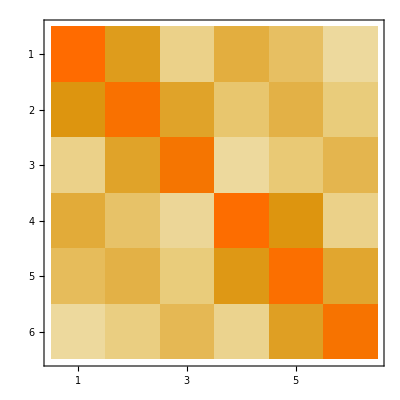

```mathematica
MatrixPlot[Abs@Zmat ]
```

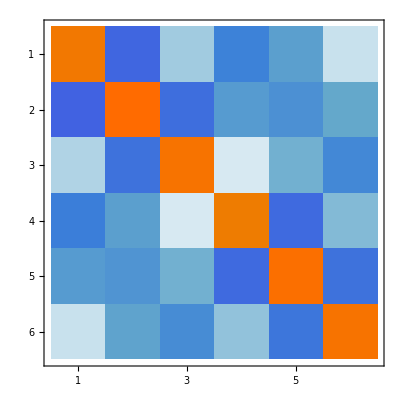

```mathematica
MatrixPlot[Im@Ymat ]
```

```mathematica
Ztotal= Zmat 1000 30.0;
```

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Aaug=ArrayFlatten[{{A,0},{0,A}}];
MatrixForm[Aaug]
```

(1 | 1 | 1 | 0 | 0 | 0
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °) | 0 | 0 | 0
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °) | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
0 | 0 | 0 | 1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Z012=Inverse[Aaug].Zmat.Aaug;
MatrixForm[Z012 1000]
```

(0.391319+1.69172 ⅈ | 0.0132835+0.000583749 ⅈ | -0.0245196-0.00789123 ⅈ | 0.29898+1.12316 ⅈ | 0.0056892+0.00482121 ⅈ | -0.0167116-0.00341302 ⅈ
-0.0245196-0.00789123 ⅈ | 0.0924605+0.492165 ⅈ | -0.029788+0.0177669 ⅈ | -0.0167116-0.00341302 ⅈ | 0.000353975+0.0233016 ⅈ | -0.0145377+0.0088572 ⅈ
0.0132835+0.000583749 ⅈ | 0.0300037+0.0169274 ⅈ | 0.0924605+0.492165 ⅈ | 0.0056892+0.00482121 ⅈ | 0.0147729+0.00818151 ⅈ | 0.000353975+0.0233016 ⅈ
0.29898+1.12316 ⅈ | 0.0056892+0.00482121 ⅈ | -0.0167116-0.00341302 ⅈ | 0.391319+1.69172 ⅈ | 0.0132835+0.000583749 ⅈ | -0.0245196-0.00789123 ⅈ
-0.0167116-0.00341302 ⅈ | 0.000353975+0.0233016 ⅈ | -0.0145377+0.0088572 ⅈ | -0.0245196-0.00789123 ⅈ | 0.0924605+0.492165 ⅈ | -0.029788+0.0177669 ⅈ
0.0056892+0.00482121 ⅈ | 0.0147729+0.00818151 ⅈ | 0.000353975+0.0233016 ⅈ | 0.0132835+0.000583749 ⅈ | 0.0300037+0.0169274 ⅈ | 0.0924605+0.492165 ⅈ)

```mathematica
MatrixForm[Abs[1000Z012[[1;;3,4;;6]]]]
```

(1.16227 | 0.00745728 | 0.0170566
0.0170566 | 0.0233043 | 0.0170234
0.00745728 | 0.0168872 | 0.0233043)

```mathematica
Y012=Inverse[Aaug].Ymat.Aaug;
MatrixForm[Y012]
```

(3.×10^-12+2.16642×10^-9 ⅈ | -8.20696×10^-11+1.911×10^-11 ⅈ | 8.20696×10^-11+1.911×10^-11 ⅈ | 1.10447×10^-26-6.94875×10^-10 ⅈ | -2.61031×10^-11-5.19343×10^-12 ⅈ | 2.61031×10^-11-5.19343×10^-12 ⅈ
8.20696×10^-11+1.911×10^-11 ⅈ | 3.×10^-12+3.33802×10^-9 ⅈ | 1.72763×10^-10-1.10226×10^-10 ⅈ | 2.61031×10^-11-5.19343×10^-12 ⅈ | -3.23117×10^-26-1.203×10^-10 ⅈ | 6.29765×10^-11-4.23626×10^-11 ⅈ
-8.20696×10^-11+1.911×10^-11 ⅈ | -1.72763×10^-10-1.10226×10^-10 ⅈ | 3.×10^-12+3.33802×10^-9 ⅈ | -2.61031×10^-11-5.19343×10^-12 ⅈ | -6.29765×10^-11-4.23626×10^-11 ⅈ | -2.58494×10^-26-1.203×10^-10 ⅈ
1.10447×10^-26-6.94875×10^-10 ⅈ | -2.61031×10^-11-5.19343×10^-12 ⅈ | 2.61031×10^-11-5.19343×10^-12 ⅈ | 3.×10^-12+2.16642×10^-9 ⅈ | -8.20696×10^-11+1.911×10^-11 ⅈ | 8.20696×10^-11+1.911×10^-11 ⅈ
2.61031×10^-11-5.19343×10^-12 ⅈ | 5.81611×10^-26-1.203×10^-10 ⅈ | 6.29765×10^-11-4.23626×10^-11 ⅈ | 8.20696×10^-11+1.911×10^-11 ⅈ | 3.×10^-12+3.33802×10^-9 ⅈ | 1.72763×10^-10-1.10226×10^-10 ⅈ
-2.61031×10^-11-5.19343×10^-12 ⅈ | -6.29765×10^-11-4.23626×10^-11 ⅈ | -1.22785×10^-25-1.203×10^-10 ⅈ | -8.20696×10^-11+1.911×10^-11 ⅈ | -1.72763×10^-10-1.10226×10^-10 ⅈ | 3.×10^-12+3.33802×10^-9 ⅈ)

```mathematica
ZposI=Z012[[2,2]]1000
```

0.0924605+0.492165 ⅈ

```mathematica
ZposII=Z012[[5,5]]1000
```

0.0924605+0.492165 ⅈ

```mathematica
YposI=Y012[[2,2]]1000
```

3.×10^-9+3.33802×10^-6 ⅈ

```mathematica
YposII=Y012[[5,5]]1000
```

3.×10^-9+3.33802×10^-6 ⅈ

```mathematica
ZcI= Sqrt[ZposI/YposI]
```

385.674-35.7383 ⅈ

```mathematica
ZcII= Sqrt[ZposII/YposII]
```

385.674-35.7383 ⅈ

```mathematica
Pn=230^2/ZcI
```

135.995+12.6019 ⅈ

```mathematica
T={{0,1,0},{0,0,1},{1,0,0}};
```

```mathematica
R=ArrayFlatten[{{T,0},{0,T}}];
```

```mathematica
MatrixForm[Inverse[R]]
```

(0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)

```mathematica
Ztrans=Inverse[R].Zmat.R
```

{{0.000200925+0.000884107 ⅈ,0.0000999152+0.00036468 ⅈ,0.000103437+0.000413854 ⅈ,0.00010848+0.000382141 ⅈ,0.0000998478+0.000349087 ⅈ,0.000103295+0.00037183 ⅈ},{0.0000999152+0.00036468 ⅈ,0.000184661+0.000898712 ⅈ,0.0000955069+0.000421026 ⅈ,0.0000998478+0.000349087 ⅈ,0.0000926263+0.00039654 ⅈ,0.0000954839+0.000378943 ⅈ},{0.000103437+0.000413854 ⅈ,0.0000955069+0.000421026 ⅈ,0.000190654+0.000893237 ⅈ,0.000103295+0.00037183 ⅈ,0.0000954839+0.000378943 ⅈ,0.000098582+0.000391084 ⅈ},{0.00010848+0.000382141 ⅈ,0.0000998478+0.000349087 ⅈ,0.000103295+0.00037183 ⅈ,0.000200925+0.000884107 ⅈ,0.0000999152+0.00036468 ⅈ,0.000103437+0.000413854 ⅈ},{0.0000998478+0.000349087 ⅈ,0.0000926263+0.00039654 ⅈ,0.0000954839+0.000378943 ⅈ,0.0000999152+0.00036468 ⅈ,0.000184661+0.000898712 ⅈ,0.0000955069+0.000421026 ⅈ},{0.000103295+0.00037183 ⅈ,0.0000954839+0.000378943 ⅈ,0.000098582+0.000391084 ⅈ,0.000103437+0.000413854 ⅈ,0.0000955069+0.000421026 ⅈ,0.000190654+0.000893237 ⅈ}}

```mathematica
Z012t=Inverse[Aaug].Inverse[R].Zmat.R.Aaug;
MatrixForm[Z012t]
```

(0.000391319+0.00169172 ⅈ | -6.13623×10^-6-0.0000117958 ⅈ | 0.0000190938-0.000017289 ⅈ | 0.00029898+0.00112316 ⅈ | 1.33069×10^-6-7.33759×10^-6 ⅈ | 0.0000113116-0.0000127662 ⅈ
0.0000190938-0.000017289 ⅈ | 0.0000924605+0.000492165 ⅈ | 0.0000302806+0.0000169138 ⅈ | 0.0000113116-0.0000127662 ⅈ | 3.53975×10^-7+0.0000233016 ⅈ | 0.0000149394+8.16144×10^-6 ⅈ
-6.13623×10^-6-0.0000117958 ⅈ | -0.0000296614+0.0000175203 ⅈ | 0.0000924605+0.000492165 ⅈ | 1.33069×10^-6-7.33759×10^-6 ⅈ | -0.0000144719+8.70299×10^-6 ⅈ | 3.53975×10^-7+0.0000233016 ⅈ
0.00029898+0.00112316 ⅈ | 1.33069×10^-6-7.33759×10^-6 ⅈ | 0.0000113116-0.0000127662 ⅈ | 0.000391319+0.00169172 ⅈ | -6.13623×10^-6-0.0000117958 ⅈ | 0.0000190938-0.000017289 ⅈ
0.0000113116-0.0000127662 ⅈ | 3.53975×10^-7+0.0000233016 ⅈ | 0.0000149394+8.16144×10^-6 ⅈ | 0.0000190938-0.000017289 ⅈ | 0.0000924605+0.000492165 ⅈ | 0.0000302806+0.0000169138 ⅈ
1.33069×10^-6-7.33759×10^-6 ⅈ | -0.0000144719+8.70299×10^-6 ⅈ | 3.53975×10^-7+0.0000233016 ⅈ | -6.13623×10^-6-0.0000117958 ⅈ | -0.0000296614+0.0000175203 ⅈ | 0.0000924605+0.000492165 ⅈ)

```mathematica
MatrixForm[Z012t[[1;;3,4;;6]]]
```

(0.00029898+0.00112316 ⅈ | 1.33069×10^-6-7.33759×10^-6 ⅈ | 0.0000113116-0.0000127662 ⅈ
0.0000113116-0.0000127662 ⅈ | 3.53975×10^-7+0.0000233016 ⅈ | 0.0000149394+8.16144×10^-6 ⅈ
1.33069×10^-6-7.33759×10^-6 ⅈ | -0.0000144719+8.70299×10^-6 ⅈ | 3.53975×10^-7+0.0000233016 ⅈ)

```mathematica
MatrixForm[Abs@1000Z012t[[1;;3,4;;6]]]
```

(0.29898+1.12316 ⅈ | 0.00133069-0.00733759 ⅈ | 0.0113116-0.0127662 ⅈ
0.0113116-0.0127662 ⅈ | 0.000353975+0.0233016 ⅈ | 0.0149394+0.00816144 ⅈ
0.00133069-0.00733759 ⅈ | -0.0144719+0.00870299 ⅈ | 0.000353975+0.0233016 ⅈ)